```mathematica
testImg=-Graphics-;
```

```mathematica
imgData=ImageData[testImg];
```

```mathematica
imgData⟦All,600⟧⟦324;;361⟧
```

{{0.25098,0.564706,0.858824},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{0.901961,0.901961,0.901961},{0.701961,0.709804,0.623529}}

```mathematica
imgData⟦324;;361,600⟧
```

{{0.25098,0.564706,0.858824},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{1.,1.,1.},{0.901961,0.901961,0.901961},{0.701961,0.709804,0.623529}}

```mathematica
Last@Position[imgData⟦1;;1920/2,600⟧,{1.,1.,1.}]
```

{359}

```mathematica
FirstPosition[imgData⟦960;;1920,600⟧,{1.,1.,1.}]
```

{482}

```mathematica
Image[imgData⟦359;;482+960,All⟧]
```

```mathematica
firstconverter[img_]:=Module[{imgData,upBorder,downBorder},
imgData=ImageData[img];
upBorder=Last@Position[imgData⟦1;;960,600⟧,{1.,1.,1.}];
downBorder=FirstPosition[imgData⟦960;;1920,600⟧,{1.,1.,1.}];
Return@Image[imgData⟦upBorder⟦1⟧;;960+downBorder⟦1⟧,All⟧];
];
```

```mathematica
AbsoluteTiming@firstconverter[testImg]
```

{0.0593886,-Graphics-}

```mathematica
1920/2//N
```

960.

```mathematica
graphPlot[img_]:=Module[{imgData,plotData},
imgData=ImageData[img];
plotData=Table[{i,Total[imgData⟦All,600⟧⟦i⟧]},{i,320,365}];
ListPlot[Labeled[#,#⟦1⟧]&/@plotData,PlotRange->Full]
];
```

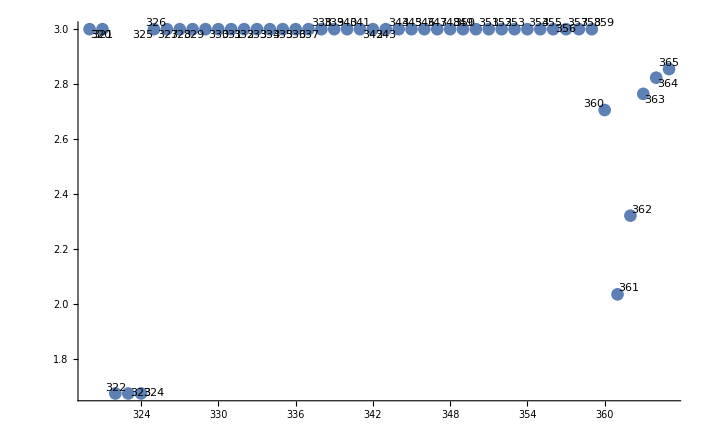

```mathematica
graphPlot[testImg]
```